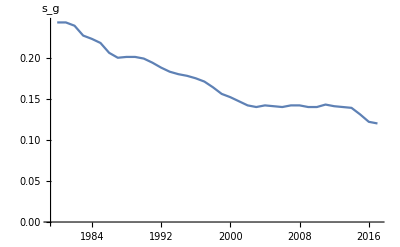

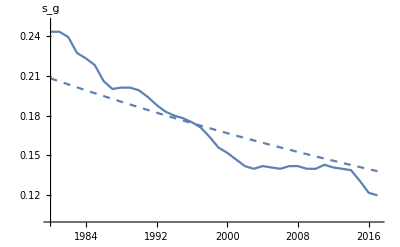

```mathematica
shares={{1980,0.243,0.757,0.757},{1981,0.243,0.757,0.761},{1982,0.239,0.761,0.767},{1983,0.227,0.773,0.781},{1984,0.223,0.777,0.767},{1985,0.218,0.782,0.759},{1986,0.206,0.794,0.769},{1987,0.200,0.800,0.774},{1988,0.201,0.799,0.778},{1989,0.201,0.799,0.781},{1990,0.199,0.801,0.787},{1991,0.194,0.806,0.800},{1992,0.188,0.812,0.806},{1993,0.183,0.817,0.803},{1994,0.180,0.820,0.795},{1995,0.178,0.822,0.790},{1996,0.175,0.825,0.788},{1997,0.171,0.829,0.781},{1998,0.164,0.836,0.774},{1999,0.156,0.844,0.770},{2000,0.152,0.848,0.769},{2001,0.147,0.853,0.777},{2002,0.142,0.858,0.789},{2003,0.140,0.860,0.792},{2004,0.142,0.858,0.788},{2005,0.141,0.859,0.779},{2006,0.140,0.860,0.775},{2007,0.142,0.858,0.780},{2008,0.142,0.858,0.794},{2009,0.140,0.860,0.819},{2010,0.140,0.860,0.831},{2011,0.143,0.857,0.823},{2012,0.141,0.859,0.815},{2013,0.140,0.860,0.805},{2014,0.139,0.861,0.798},{2015,0.131,0.869,0.793},{2016,0.122,0.878,0.795},{2017,0.120,0.880,0.797}};

ListPlot[shares[[All,{1,2}]],(*Selecting years and s_g values*)Joined->True, AxesLabel->{Null,"s_g"}]

Plot[sg[t],{t,1980,2017},AxesLabel->{Null,"s_g"},PlotStyle->Dashed,PlotRange->{{1980, 2017},{0.1,0.25}}];

Show[%,%%]
```

```mathematica
e[1980]/y[1980]
```

0.732987